# 0) Preliminaries

```mathematica
plotFun[fun_,lims_,epilog_,label_,legs_:None]:=Framed@Plot[fun,{x,lims[[1,1]],lims[[1,2]]},PlotRange->{Full,{lims[[2,1]],lims[[2,2]]}},Epilog->epilog,PlotLegends->legs,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"x","y"},BaseStyle->{FontSize->20}]
```

```mathematica
discPlotFun[fun_,range_,lims_,epilog_,label_]:=Framed@DiscretePlot[fun,{n,range[[1]],range[[2]]},PlotRange->lims,Epilog->epilog,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"M","y"},BaseStyle->{FontSize->20}]
```

```mathematica
(*ClearAll[plotLimitDisc]
plotLimitDisc[fun_,n0fun_,epsran_,maxran_,limit_,label_,seqname_:"a_n",epilog_:{},limpos_:Automatic]:=Module[{funplot,epsplot,ilimpos=limpos},
If[ilimpos===Automatic,ilimpos={22,limit+05}];
funplot=DiscretePlot[fun[n],{n,1,maxran},PlotRange->{Full,All},Filling->None,Epilog->epilog,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"n","y"},BaseStyle->{FontSize->20}];
epsplot[ϵ_]:=Graphics[{{Line[{{1,limit},{maxran,limit}}],Arrow[{ilimpos-{0.5,0}(*{(*maxran-20*)20,limit+.05}*),{(*maxran-25*)(*15*)ilimpos[[1]]-5,limit}}],Text["lim_(n → ∞) "<>seqname<>"="<>ToString[limit],ilimpos(*{(*maxran-20*)22,limit+.05}*),Left]},{Thick,Orange,Line[{{0,limit-ϵ},{maxran,limit-ϵ}}]},{Arrowheads[{-.03,.03}],Arrow[{{5,limit},{5,limit-ϵ}}],Text[Style["ϵ",20],{4,limit-ϵ/2}]},{Opacity[.5],Orange,Rectangle[{0,limit-ϵ},{maxran,limit}]},Module[{n0=n0fun[ϵ]},{Line[{{n0,fun[n0]},{n0,0}}],Text[Style["n_0= "<>ToString[n0fun[ϵ]],20],{n0+1.5,.05},Left]}]}];
Manipulate[
Column[{
Show[funplot,epsplot[ϵ],epilog,PlotRange->{{0,maxran},All}],
Item[Style["ϵ = "<>ToString[ϵ],30],ItemSize->{All,4},Background->LightOrange]
},Frame->All],
{{ϵ,epsran[[2]]},epsran[[1]],epsran[[2]],Appearance->"Open" }
]
]*)
```

```mathematica
(*ClearAll[plotLimitDisc]
plotLimitDisc[fun_,n0fun_,epsran_,maxran_,limit_,label_,upreg_:True,lowreg_:True,seqname_:"a_n",epilog_:{},limpos_:Automatic]:=Module[{funplot,epsplot,ilimpos=limpos},
If[ilimpos===Automatic,ilimpos={22,limit+05}];
funplot=DiscretePlot[fun[n],{n,1,maxran},PlotRange->{Full,All},Filling->None,Epilog->epilog,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"n","y"},BaseStyle->{FontSize->20}];
epsplot[ϵ_]:=Graphics[{
(*limit line and label*)
{Line[{{1,limit},{maxran,limit}}],Arrow[{ilimpos-{0.5,0},{ilimpos[[1]]-5,limit}}],Text["lim_(n → ∞) "<>seqname<>"="<>ToString[limit],ilimpos,Left]},

(*lower region*)
If[upreg,{{Thick,Orange,Line[{{0,limit-ϵ},{maxran,limit-ϵ}}]},{Arrowheads[{-.03,.03}],Arrow[{{5,limit},{5,limit-ϵ}}],Text[Style["ϵ",20],{4,limit-ϵ/2}]},{Opacity[.5],Orange,Rectangle[{0,limit-ϵ},{maxran,limit}]}},{}],

(*upper region*)
If[lowreg,{{Thick,Orange,Line[{{0,limit+ϵ},{maxran,limit+ϵ}}]},{Arrowheads[{-.03,.03}],Arrow[{{5,limit},{5,limit+ϵ}}],Text[Style["ϵ",20],{4,limit+ϵ/2}]},{Opacity[.5],Orange,Rectangle[{0,limit+ϵ},{maxran,limit}]}},{}],

(*moving n0*)
Module[{n0=n0fun[ϵ]},{Line[{{n0,fun[n0]},{n0,0}}],Text[Style["n_0= "<>ToString[n0fun[ϵ]],20],{n0+1.5,.05},Left]}]
}];
Manipulate[
Column[{
Show[funplot,epsplot[ϵ],epilog,PlotRange->{{0,maxran},All}],
Item[Style["ϵ = "<>ToString[ϵ],30],ItemSize->{All,4},Background->LightOrange]
},Frame->All],
{{ϵ,epsran[[2]]},epsran[[1]],epsran[[2]],Appearance->"Open" }
]
]*)
```

```mathematica
ClearAll[plotLimitDisc]
plotLimitDisc[fun_,n0fun_,epsran_,maxran_,limit_,label_,upreg_:True,lowreg_:True,seqname_:"a_n",epilog_:{},limpos_:Automatic]:=Module[{funplot,epsplot,ilimpos=limpos},
Manipulate[
Column[{
Show[funplot,epsplot[ϵ],epilog,PlotRange->{{0,maxran},All}],
Item[Style["ϵ = "<>ToString[ϵ],30],ItemSize->{All,4},Background->LightOrange]
},Frame->All],
{{ϵ,epsran[[2]]},epsran[[1]],epsran[[2]],Appearance->"Open" },
{{funplot,DiscretePlot[fun[n],{n,1,maxran},PlotRange->{Full,All},Filling->None,Epilog->epilog,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"n","y"},BaseStyle->{FontSize->20}]},{0,1},ControlType->None},
{{ilimpos,If[limpos===Automatic,{22,limit+05},limpos]},ControlType->None},
SaveDefinitions->True,Initialization:>{epsplot[ϵ_]:=Graphics[{
(*limit line and label*)
{Line[{{1,limit},{maxran,limit}}],Arrow[{ilimpos-{0.5,0},{ilimpos[[1]]-5,limit}}],Text["lim_(n → ∞) "<>seqname<>"="<>ToString[limit],ilimpos,Left]},

(*lower region*)
If[upreg,{{Thick,Orange,Line[{{0,limit-ϵ},{maxran,limit-ϵ}}]},{Arrowheads[{-.03,.03}],Arrow[{{5,limit},{5,limit-ϵ}}],Text[Style["ϵ",20],{4,limit-ϵ/2}]},{Opacity[.5],Orange,Rectangle[{0,limit-ϵ},{maxran,limit}]}},{}],

(*upper region*)
If[lowreg,{{Thick,Orange,Line[{{0,limit+ϵ},{maxran,limit+ϵ}}]},{Arrowheads[{-.03,.03}],Arrow[{{5,limit},{5,limit+ϵ}}],Text[Style["ϵ",20],{4,limit+ϵ/2}]},{Opacity[.5],Orange,Rectangle[{0,limit+ϵ},{maxran,limit}]}},{}],

(*moving n0*)
Module[{n0=n0fun[ϵ]},{Line[{{n0,fun[n0]},{n0,0}}],Text[Style["n_0= "<>ToString[n0fun[ϵ]],20],{n0+1.5,.05},Left]}]
}]}
]
]
```

# 1) Konvergenzradien

a) f(x)=∑_(n=0)^∞ x^n/(√(n+1))

b) sin(x)=∑_(n=0)^∞ (-1)^n x^(2n+1)/((2n+1)!)

#### Useful formulas

Quotientenkriterium I

∀n≥n_0: a_n≠0  ∧  Abs[a_(n+1)]/Abs[a_n]≤θ, 0<θ<1  ⇒   ∑_(n=1)^∞ a_n absolut konvergent

Quotientenkriterium II

a_n≠0, lim_(n→∞) Abs[a_(n+1)]/Abs[a_n]=θ  ⇒
θ<1:   ∑_(n=1)^∞ a_n absolut konvergent
θ>1:   ∑_(n=1)^∞ a_n divergent

## Solution

## a)

Quotientenkriterium:

a_n:=x^n/(√(n+1))

It holds that a_n≠0 for x≠0 and lim_(n→∞) Abs[a_(n+1)]/Abs[a_n]=lim_(n→∞) (Abs[x]^(n+1)/(√(n+2)))/(Abs[x]^n/(√(n+1)))=Abs[x]·lim_(n→∞) (√(n+1))/(√(n+2))=Abs[x]·lim_(n→∞) √((1+1/n)/(1+2/n))=Abs[x]=θ

That is, for Abs[x]<1 converges absolutely, for Abs[x]>1 diverges and the Konvergenzradius is thus R=1.

## b)

Quotientenkriterium:

a_n:=(-1)^n x^(2n+1)/((2n+1)!)

It holds that a_n≠0 for x≠0 and lim_(n→∞) Abs[a_(n+1)]/Abs[a_n]=lim_(n→∞) (Abs[x]^(2n+3)/((2n+3)!))/(Abs[x]^(2n+1)/((2n+1)!))=Abs[x]^2·lim_(n→∞) ((2n+1)!)/((2n+3)!)=Abs[x]^2·lim_(n→∞) 1/((2n+3)(2n+2))=Abs[x]^2·lim_(n→∞) 1/(n^2(2+3/n)(2+2/n))=0=θ.

As θ<1 for arbitrary x, the Reihe converges absolutely for all x∈ℝ and the Konvergenzradius is R=∞.

# 2) Logarithmus

a) ln(1/x)=-ln(x)

b) ln(ⅇ)=1

c) ln(1)=0

#### Useful formulas

Properties of exponential function

exp(-x)=1/(exp(x))
exp(1)=ⅇ
exp(0)=1

## Solution

## a)

Let y:=exp(-x). Then ln(y)=-x from the definition of the logarithm and also 1/y=exp(x) from the first property of exp mentioned in “Useful formulas” section. From the definition thus ln(1/y)=x. This formula, together with -ln(y)=x, gives ln(1/y)=-ln(y) as we were to prove.

## b)

From the formula exp(1)=ⅇ and the definition of the logarithm we get immediately 1=ln(ⅇ).

## c)

From the formula exp(0)=1 and the definition of the logarithm we get immediately 0=ln(1).

# 3) Sinh

sinh: ℝ→ℝ
sinh(x):=1/2(ⅇ^x-ⅇ^-x)

a) Strictly monotonically increasing?

b) Bijective?

c) Inverse function: arsinh(x)=ln(x+√(1+x^2))  ?

## Solution

## a) Strictly monotonically increasing?

Let x'>x. Is it true that 1/2(ⅇ^x'-ⅇ^-x')>1/2(ⅇ^x-ⅇ^-x)?

1/2(ⅇ^x'-ⅇ^-x')>1/2(ⅇ^x-ⅇ^-x) ⇔ ⅇ^x'-ⅇ^x>ⅇ^-x'-ⅇ^-x

Moreover, ⅇ^-x'-ⅇ^-x=1/ⅇ^x'-1/ⅇ^x=(ⅇ^x-ⅇ^x')/(ⅇ^x ⅇ^x')=-(ⅇ^x'-ⅇ^x)/(ⅇ^x ⅇ^x'). Also:

x'>x  and thus ⅇ^x'-ⅇ^x>0 due to monotonicity of exp. Therefore:

ⅇ^x'-ⅇ^x>-(ⅇ^x'-ⅇ^x)/(ⅇ^x ⅇ^x') ⇔ 1>-1/(ⅇ^x ⅇ^x') ⇔ ⅇ^(x+x')>-1

The last inequality is definitely true and the sinh function is indeed strictly monotonically increasing.

## b) Bijective?

The function is strictly monotonically increasing, therefore injective. Let check whether it is also surjective. Let y∈ℝ, then we look for such x that satisfies:

y=sinh(x)=1/2(ⅇ^x-ⅇ^-x)

So: 2y=ⅇ^x-1/ⅇ^x ⇔ 0=(ⅇ^x)^2+(-2y)ⅇ^x+(-1). This is a quadratic polynomial in ⅇ^x and so:

ⅇ^x=(2y+√(4 y^2+4))/2=y+√(y^2+1)

Finally, from the definition of the logarithm:

x=ln(y+√(y^2+1))

To conclude, for arbitrary y∈ℝ we can define x=ln(y+√(y^2+1)), such that sinh(x)=y and the function is therefore surjective.

The function is injective and surjective, therefore bijective. We also found the formula for the inverse function: x=ln(y+√(y^2+1)).

## c) Inverse function?

In the following, basically the same as in b) is done, but using a different approach.

The sinh function is defined for all x∈ℝ. Let us find the Definitionsbereich for arsihn. The Zielmenge of exp is ℝ^+, so the logarithm is defined only for positive numbers. The argument in the definition of arsinh function satisfies x+√(1+x^2)>x+√(x^2)=x+Abs[x]≥0 and the arsinh is therefore defined for all x∈ℝ.

For arbitrary x∈ℝ we can therefore perform the following calculation:

sinh(arsinh(x))=1/2(ⅇ^(ln(x+√(1+x^2)))-ⅇ^(-ln(x+√(1+x^2))))=1/2((x+√(1+x^2))-1/(ⅇ^(ln(x+√(1+x^2)))))=1/2((x+√(1+x^2))-1/(x+√(1+x^2)))=1/2(((x+√(1+x^2))^2-1)/(x+√(1+x^2)))=1/2((x^2+2x √(1+x^2)+(1+x^2) -1)/(x+√(1+x^2)))=1/2((2 x^2+2x √(1+x^2))/(x+√(1+x^2)))=(x(x+√(1+x^2)))/(x+√(1+x^2))=x

And so sinh(arsinh(x))=x for all x∈ℝ. Similarly:

arsinh(sinh(x))=ln(1/2(ⅇ^x-ⅇ^-x)+√(1+(1/2(ⅇ^x-ⅇ^-x))^2))=ln(1/2(ⅇ^x-ⅇ^-x)+√(1+(ⅇ^(2x)-2+ⅇ^(-2x))/4))=ln(1/2(ⅇ^x-ⅇ^-x)+√((ⅇ^(2x)+2+ⅇ^(-2x))/4))=ln(1/2(ⅇ^x-ⅇ^-x)+√((1/2(ⅇ^x+ⅇ^-x))^2))=ln(1/2(ⅇ^x-ⅇ^-x)+1/2(ⅇ^x+ⅇ^-x))=ln(ⅇ^x)=x

And so arsinh(sinh(x))=x for all x∈ℝ.

In total, this means that both sinh and arsinh are bijective and inverse to each other.

# 4) Cauchy-Produkt

a_n:=b_n:=(-1)^n/(√(n+1))

c_n:=∑_(k=0)^n a_(n-k)b_k

a) ∑_(n=0)^∞ a_n, ∑_(n=0)^∞ b_n converge?

c) ∑_(n=0)^∞ c_n diverges?

d) (∑_(n=0)^∞ x^n/(√(n+1)))^2 for x=-1 ?

#### Useful formulas

Leibnitz Kriterium

a_n↘ 0    ⇒   ∑_(n=1)^∞ (-1)^n a_n konvergent

Mean inequality

∀a,b∈ℝ^+:   √(a b)≤(a+b)/2

Satz 7.3

∑_(n=1)^∞ a_n konvergent ⇒ a_n→0

## Solution

## a)

Does ∑_(n=0)^∞ (-1)^n/(√(n+1)) converge?

Leibnitz Kriterium: ∑_(n=0)^∞ (-1)^n d_n , where d_n:=1/(√(n+1)). It is easy to check that d_n↘ 0 and thus ∑_(n=0)^∞ a_n=∑_(n=0)^∞ b_n indeed converges.

## b)

∑_(n=0)^∞ c_n=∑_(n=0)^∞ ∑_(k=0)^n a_(n-k)b_k=∑_(n=0)^∞ ∑_(k=0)^n (-1)^(n-k)/(√(n-k+1))(-1)^k/(√(k+1))=∑_(n=0)^∞ ∑_(k=0)^n (-1)^n/(√((n-k+1)(k+1)))=∑_(n=0)^∞ (-1)^n∑_(k=0)^n 1/(√((n-k+1)(k+1)))

Moreover:

√(a b)≤(a+b)/2 ⇔ 2/(a+b)≤1/(√(a b))

and so:

∑_(k=0)^n 1/(√((n-k+1)(k+1)))≤∑_(k=0)^n 2/((n-k+1)+(k+1))=∑_(k=0)^n 2/(n+2)=(2(n+1))/(n+2)

Therefore:

∑_(n=0)^∞ c_n≥∑_(n=0)^∞ (-1)^n(2(n+1))/(n+2)

But:

lim_(n→∞) Abs[((-1)^n (2 (n+1)))/(n+2)]=2·lim_(n→∞) (n+1)/(n+2)=2≠ 0

Because the individual terms do not converge to zero, the whole Reihe ∑_(n=0)^∞ c_n diverges.

## c)

First, we have to calculate ∑_(n=0)^∞ x^n/(√(n+1)) for x=-1 and then square the result. We cannot simplify expression (∑_(n=0)^∞ x^n/(√(n+1)))^2 and then calculate its value for x=-1.

# 5) Spirale

Z: ℝ^+→ℂ
ω,γ∈ℝ

Z(t)=exp((ⅈω+γ)t)
x(t)=Im(Z(t))

a) Meaning and role of γ?

b) Behavior of x(t) for γ<0?

## Plots

## Z(t)

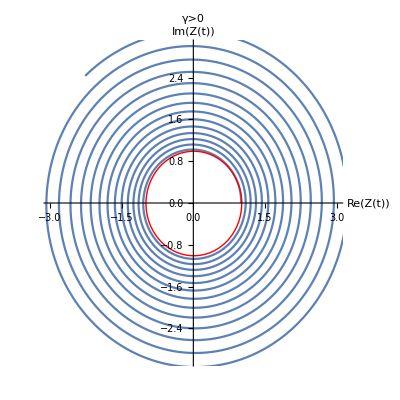

```mathematica
Framed@With[{γ=+.2,ω=14},ParametricPlot[ReIm@Exp[γ t+I ω t],{t,0,6},PlotLabel->Framed@Style["γ>0",Black,Bold,20],ImageSize->400,AxesLabel->{"Re(Z(t))","Im(Z(t))"},BaseStyle->{FontSize->20},PlotRange->3,Epilog->{Red,Thick,Circle[{0,0},1]}]]
```

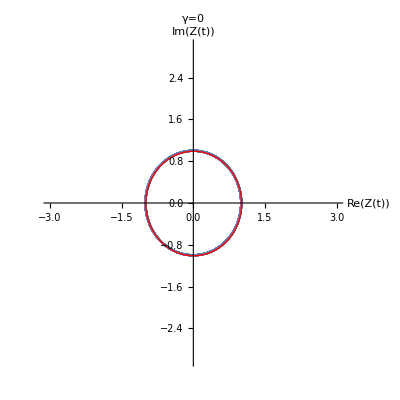

```mathematica
Framed@With[{γ=0,ω=14},ParametricPlot[ReIm@Exp[γ t+I ω t],{t,0,6},PlotLabel->Framed@Style["γ=0",Black,Bold,20],ImageSize->400,AxesLabel->{"Re(Z(t))","Im(Z(t))"},BaseStyle->{FontSize->20},PlotRange->3,Epilog->{Red,Thick,Circle[{0,0},1]}]]
```

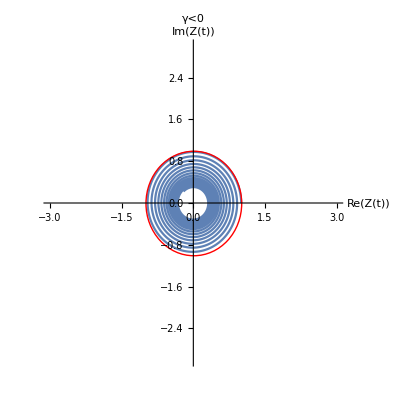

```mathematica
Framed@With[{γ=-.2,ω=14},ParametricPlot[ReIm@Exp[γ t+I ω t],{t,0,6},PlotLabel->Framed@Style["γ<0",Black,Bold,20],ImageSize->400,AxesLabel->{"Re(Z(t))","Im(Z(t))"},BaseStyle->{FontSize->20},PlotRange->3,Epilog->{Red,Thick,Circle[{0,0},1]}]]
```

## x(t)

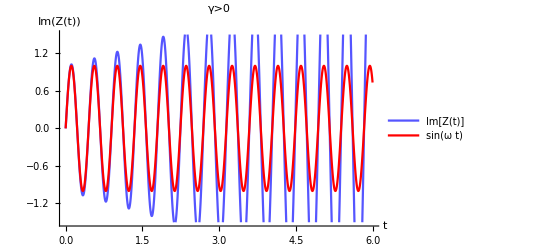

```mathematica
Framed@With[{γ=+.2,ω=14},Plot[{Im@Exp[γ t+I ω t],Sin[ω t]},{t,0,6},PlotLabel->Framed@Style["γ>0",Black,Bold,20],ImageSize->400,AxesLabel->{"t","Im(Z(t))"},BaseStyle->{FontSize->20},PlotRange->{All,{-1.5,1.5}},PlotStyle->{Lighter@Blue,Red},PlotLegends->{"Im[Z(t)]","sin(ω t)"}]]
```

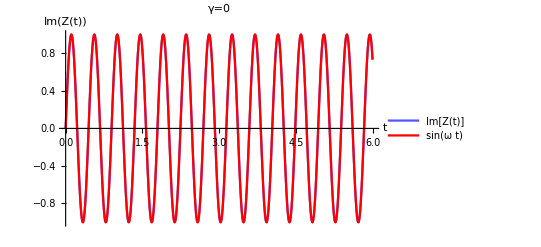

```mathematica
Framed@With[{γ=+0,ω=14},Plot[{Im@Exp[γ t+I ω t],Sin[ω t]},{t,0,6},PlotLabel->Framed@Style["γ=0",Black,Bold,20],ImageSize->400,AxesLabel->{"t","Im(Z(t))"},BaseStyle->{FontSize->20},PlotRange->{All,1.5},PlotStyle->{Lighter@Blue,Red},PlotLegends->{"Im[Z(t)]","sin(ω t)"}]]
```

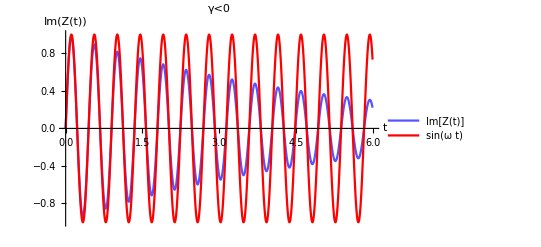

```mathematica
Framed@With[{γ=-.2,ω=14},Plot[{Im@Exp[γ t+I ω t],Sin[ω t]},{t,0,6},PlotLabel->Framed@Style["γ<0",Black,Bold,20],ImageSize->400,AxesLabel->{"t","Im(Z(t))"},BaseStyle->{FontSize->20},PlotRange->{All,1.5},PlotStyle->{Lighter@Blue,Red},PlotLegends->{"Im[Z(t)]","sin(ω t)"}]]
```

## Solution

## a)

Z(t)=exp((ⅈω+γ)t)=ⅇ^(γ t)·ⅇ^(ⅈ ω t) and so:

|Z(t)|= ⅇ^(γ t)  and  Arg(Z(t))=ω t

So the plot of Z(t) in a complex plane is a spiral, whose winding rate is characterized by ω and its growing rate is characterized by γ. Let us discuss possible values of parameter γ:

γ<0: the spiral is growing smaller and smaller until it reaches the Ursprung for t→∞

γ=0: degenerate case, where the Radius stays constant and we have a circle, not a spiral

γ>0: the spiral is growing larger and larger as t→∞

## b)

x(t)=Im(Z(t))=ⅇ^(γ t)·Im(ⅇ^(ⅈ ω t))=ⅇ^(γ t)·sin(ω t)

The function x(t) describes the time evolution of a position of the linear harmonic oscillator, where γ plays the role of the dumping constant (when γ<0).